```mathematica
it
```

```mathematica
By Le Chen.
Crated on Sun 24 Apr 2022 09:06:21 AM EDT
```

```mathematica
G[t_,x_]:=1/(√(2π t))Exp[-x^2/(2 t)];
Φ[x_]:=(Erf[x/Sqrt[2]]+1)/2;
ERF[x_]:=2 Subscript[Φ, m][Sqrt[2] x]-1;
ERFC[x_]:=1-ERF[x];
```

```mathematica
θ = 2(β+γ)-2 -(β d)/α
tHat = Θ Gamma[θ+1] t^(θ+1) 
Subscript[u, 0]^2 MittagLefflerE[θ+1,λ^2 tHat ] + 2 Subscript[u, 0] Subscript[u, 1] t MittagLefflerE[θ+1,2,λ^2 tHat] + 2 Subscript[u, 1]^2 t^2 MittagLefflerE[θ+1,3,λ^2 tHat]
```

```mathematica
-2-(d β)/α+2 (β+γ)
```

t^(-1-(d β)/α+2 (β+γ)) Θ Gamma[-1-(d β)/α+2 (β+γ)]

MittagLefflerE[-1-(d β)/α+2 (β+γ),t^(-1-(d β)/α+2 (β+γ)) Θ λ^2 Gamma[-1-(d β)/α+2 (β+γ)]] u_0^2+2 t MittagLefflerE[-1-(d β)/α+2 (β+γ),2,t^(-1-(d β)/α+2 (β+γ)) Θ λ^2 Gamma[-1-(d β)/α+2 (β+γ)]] u_0 u_1+2 t^2 MittagLefflerE[-1-(d β)/α+2 (β+γ),3,t^(-1-(d β)/α+2 (β+γ)) Θ λ^2 Gamma[-1-(d β)/α+2 (β+γ)]] u_1^2

```mathematica
FullSimplify[Subscript[u, 0]^2 MittagLefflerE[θ+1,λ^2 tHat ] + 2 Subscript[u, 0] Subscript[u, 1] t MittagLefflerE[θ+1,2,λ^2 tHat] + 2 Subscript[u, 1]^2 t^2 MittagLefflerE[θ+1,3,λ^2 tHat]/.{β->2,α->2,γ->0,d->1}]
```

Cosh[t √Θ λ] u_0^2+(2 Sinh[t √Θ λ] u_0 u_1)/(√Θ λ)+2 t^2 MittagLefflerE[2,3,t^2 Θ λ^2] u_1^2

```mathematica
SHE
```

```mathematica
Θ=1/(2π)Integrate[MittagLefflerE[β,β+γ,-ν/2 Abs[ξ]^α]^2/.{β->1,α->2,γ->0},{ξ,-∞,∞},Assumptions->{ν>0}]
θ = 2(β+γ)-2 -(β d)/α/.{β->1,α->2,γ->0,d->1}
tHat = Θ Gamma[θ+1] t^(θ+1) 
Subscript[u, 0]^2 MittagLefflerE[θ+1,λ^2 tHat ] 
FullSimplify[2 α + α/β Min[2γ-1,0]/.{β->1,α->2,γ->0,d->1}]
```

1/(2 √π √ν)

-1/2

(√t)/(2 √ν)

ⅇ^((t λ^4)/(4 ν)) Erfc[-(√t λ^2)/(2 √ν)] u_0^2

2

```mathematica
ⅇ^((t λ^4)/(4 ν)) ERFC[-(√t λ^2)/(2 √ν)] Subscript[u, 0]^2//FullSimplify
```

-2 ⅇ^((t λ^4)/(4 ν)) u_0^2 (-1+Φ_m[-(√t λ^2)/(√2 √ν)])

```mathematica
MittagLefflerE[β,β+γ,-ν/2 Abs[ξ]^α]^2/.{β->1,α->2,γ->0}//FullSimplify
```

ⅇ^(-ν ξ Conjugate[ξ])

```mathematica
θ = 2(β+γ)-2 -(β d)/α
```

```mathematica
MittagLefflerE[1/2,z]
```

```mathematica
ⅇ^(z^2) ERFC[-z]
```

ⅇ^(z^2) (2-2 Φ_m[-√2 z])

```mathematica
SWE
```

```mathematica
FullSimplify[MittagLefflerE[β,β+γ,-ν/2 Abs[ξ]^α]^2/.{β->2,α->2,γ->0},Assumptions->{ν>0}]
```

(2 Sin[(√ν Abs[ξ])/(√2)]^2)/(ν Abs[ξ]^2)

```mathematica
Θ=1/(2π)Integrate[MittagLefflerE[β,β+γ,-ν/2 Abs[ξ]^α]^2/.{β->2,α->2,γ->0},{ξ,-∞,∞},Assumptions<d->{ν>0}]
θ = 2(β+γ)-2 -(β d)/α/.{β->2,α->2,γ->0,d->1}
tHat = Θ Gamma[θ+1] t^(θ+1) 

FullSimplify[Subscript[u, 0]^2 MittagLefflerE[θ+1,λ^2 tHat ] + 2 Subscript[u, 0] Subscript[u, 1] t MittagLefflerE[θ+1,2,λ^2 tHat] + 2 Subscript[u, 1]^2 t^2 (MittagLefflerE[θ+1,λ^2 tHat]-1) (λ^2 tHat)^-1//Expand,Assumptions->{ν>0,t>0,λ>0}]
FullSimplify[2 α + α/β Min[2γ-1,0]/.{β->2,α->2,γ->0,d->1}]
```

1/(√2 √ν)

1

t^2/(√2 √ν)

```mathematica
Cosh[(t λ)/(2^(1/4) ν^(1/4))] <Subscript[du, 0]^2+(2 2^(1/4) ν^(1/4) Sinh[(t λ)/(2^(1/4) ν^(1/4))] Subscript[u, 0] Subscript[u, 1])/λ+1/λ^2 2 √2 √ν (-1+Cosh[(t λ)/(2^(1/4) ν^(1/4))]) Subscript[u, 1]^2
```

3

```mathematica
Cosh[(t λ)/(2^(1/4) ν^(1/4))] Subscript[u, 0]^2+(2 2^(1/4) ν^(1/4) Sinh[(t λ)/(2^(1/4) ν^(1/4))] Subscript[u, 0] Subscript[u, 1])/λ+(2 √2 √ν (-1+Cosh[(t λ)/(2^(1/4) ν^(1/4))]) Subscript[u, 1]^2)/λ^2//Expand
```

Cosh[(t λ)/(2^(1/4) ν^(1/4))] u_0^2+(2 2^(1/4) ν^(1/4) Sinh[(t λ)/(2^(1/4) ν^(1/4))] u_0 u_1)/λ-(2 √2 √ν u_1^2)/λ^2+(2 √2 √ν Cosh[(t λ)/(2^(1/4) ν^(1/4))] u_1^2)/λ^2

```mathematica
1/(2π)Integrate[MittagLefflerE[2,2,-ξ^2],{ξ,-∞,∞}]
```

1/2

```mathematica
MittagLefflerE[3/2,x]//FullSimplify
```

```mathematica
MittagLefflerE[1/4,x]
```

```mathematica
MittagLefflerE[1/2,x]//FullSimplify
```

ⅇ^(x^2) (1+Erf[x])

```mathematica
Fractional SHE
```

```mathematica
MittagLefflerE[β,β+γ,-ν/2 Abs[ξ]^α]^2/.{β->1,γ->0}//FullSimplify
```

```mathematica
ⅇ^(-ν Abs[ξ]^α)<d
```

```mathematica
Θ=1/(2π)Integrate[MittagLefflerE[β,β+γ,-ν/2 Abs[ξ]^α]^2/.{β->1,γ->0},{ξ,-∞,∞},Assumptions->{ν>0,0<α≤2}]
θ = 2(β+γ)-2 -(β d)/α/.{β->1,γ->0,d->1}
tHat = Θ Gamma[θ+1] t^(θ+1) 
FullSimplify[2 α + α/β Min[2γ-1,0]/.{β->1,γ->0,d->1}]
```

(ν^(-1/α) Gamma[1+1/α])/π

-1/α

(t^(1-1/α) ν^(-1/α) Gamma[1-1/α] Gamma[1+1/α])/π

α

```mathematica
Fractional SWE
```

```mathematica
FullSimplify[MittagLefflerE[β,β+γ,-ν/2 Abs[ξ]^α]^2/.{β->2,γ->0},Assumptions->{0<α≤2,ξ >0}]
```

(2 ξ^-α Sin[(√ν ξ^(α/2))/(√2)]^2)/ν

```mathematica
Θ=1/π Integrate[MittagLefflerE[β,β+γ,-ν/2 ξ^α]^2/.{β->2,γ->0},{ξ,0,∞},Assumptions->{ν>0,1<α≤2}]
θ = 2(β+γ)-2 -(β d)/α/.{β->2,γ->0,d->1}
tHat = Θ Gamma[θ+1] t^(θ+1) 

FullSimplify[Subscript[u, 0]^2 MittagLefflerE[θ+1,λ^2 tHat ] + 2 Subscript[u, 0] Subscript[u, 1] t MittagLefflerE[θ+1,2,λ^2 tHat] + 2 Subscript[u, 1]^2 t^2 (MittagLefflerE[θ+1,λ^2 tHat]-1/Gamma[β]) (λ^2 tHat)^-1/.β->2//Expand,Assumptions->{ν>0,t>0,λ ∈Reals, Subscript[u, 0]>0, Subscript[u, 1]>0}]
```

(2^(2-1/α) ν^(-1/α) Cos[π/α] Gamma[-2+2/α])/(π α)

2-2/α

(2^(2-1/α) t^(3-2/α) ν^(-1/α) Cos[π/α] Gamma[3-2/α] Gamma[-2+2/α])/(π α)

1/(t λ^2)(u_1 (2 t^2 λ^2 MittagLefflerE[3-2/α,2,(2^((-1+α)/α) t^(3-2/α) λ^2 ν^(-1/α) Csc[π/α])/α] u_0-2^(1/α) t^(2/α) α ν^(1/α) Sin[π/α] u_1)+MittagLefflerE[3-2/α,(2^((-1+α)/α) t^(3-2/α) λ^2 ν^(-1/α) Csc[π/α])/α] (t λ^2 u_0^2+2^(1/α) t^(2/α) α ν^(1/α) Sin[π/α] u_1^2))

```mathematica
Θ=1/π Integrate[MittagLefflerE[β,β+γ,-ν/2 ξ^α]^2/.{β->2,γ->0},{ξ,0,∞},Assumptions->{ν>0,1<α≤2}]
θ = 2(β+γ)-2 -(β d)/α/.{β->2,γ->0,d->1}
tHat = Θ Gamma[θ+1] t^(θ+1) 

FullSimplify[<Subscript[du, 0]^2 MittagLefflerE[θ+1,λ^2 tHat ] + 2 Subscript[u, 0] Subscript[u, 1] t MittagLefflerE[θ+1,2,λ^2 tHat] + 2 Subscript[u, 1]^2 t^2 (MittagLefflerE[θ+1,λ^2 tHat]-1/Gamma[β]) (λ^2 tHat)^-1/.β->2//Expand,Assumptions->{ν>0,t>0,λ ∈Reals, Subscript[u, 0]>0, Subscript[u, 1]>0}]//Expand
```

(2^(2-1/α) ν^(-1/α) Cos[π/α] Gamma[-2+2/α])/(π α)

2-2/α

(2^(2-1/α) t^(3-2/α) ν^(-1/α) Cos[π/α] Gamma[3-2/α] Gamma[-2+2/α])/(π α)

```mathematica
MittagLefflerE[3-2/α,(2^((-1+α)/α) t^(3-2/α) λ^2 ν^(-1/α) Csc[π/α])/(<dα)] Subscript[u, 0]^2+2 t MittagLefflerE[3-2/α,2,(2^((-1+α)/α) t^(3-2/α) λ^2 ν^(-1/α) Csc[π/α])/α] Subscript[u, 0] Subscript[u, 1]-(2^(1/α) t^(-1+2/α) α ν^(1/α) Sin[π/α] Subscript[u, 1]^2)/λ^2+1/λ^2 2^(1/α) t^(-1+2/α) α ν^(1/α) MittagLefflerE[3-2/α,(2^((-1+α)/α) t^(3-2/α) λ^2 ν^(-1/α) Csc[π/α])/α] Sin[π/α] Subscript[u, 1]^2
```

```mathematica
(2^(2-1/α) t^(3-2/α) ν^(-1/α) Cos[π/α] Gamma[3-2/α] Gamma[-2+2/α])/(π α)//TeXForm
```

\frac{2^{2-\frac{1}{\alpha }} \nu ^{-1/\alpha } \cos
   \left(\frac{\pi }{\alpha }\right) \Gamma
   \left(3-\frac{2}{\alpha }\right) \Gamma
   \left(\frac{2}{\alpha }-2\right) t^{3-\frac{2}{\alpha
   }}}{\pi  \alpha }

```mathematica
(2^(2-1/α) ν^(-1/α) Cos[π/α] Gamma[-2+2/α])/(π α)//TeXForm
```

\frac{2^{2-\frac{1}{\alpha }} \nu ^{-1/\alpha } \cos
   \left(\frac{\pi }{\alpha }\right) \Gamma
   \left(\frac{2}{\alpha }-2\right)}{\pi  \alpha }

```mathematica
1/π Integrate[(2 ξ^-α Sin[(√ν ξ^(α/2))/(√2)]^2)/ν,{ξ,0,∞},Assumptions->{ν>0,0<α≤2}]
```

```mathematica
1/π Integrate[(2 ξ^-α Sin[(√ν ξ^(α/2))/(√2)]^2)/ν,{ξ,0,∞},Assumptions->{ν>0,1<α≤2}]
```

```mathematica
<d
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {4.81037×10^7}. NIntegrate obtained 15.5856 and 1.8374 for the integral and error estimates.

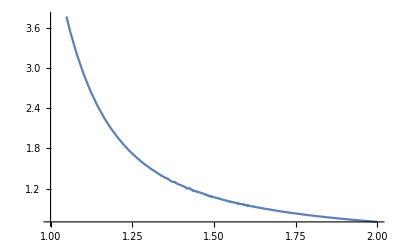

```mathematica
Plot[1/π NIntegrate[(2 ξ^-α Sin[(√ν ξ^(α/2))/(√2)]^2)/ν/.ν->1,{ξ,0,∞}],{α,1,2}]
```

```mathematica
FullSimplify[ α Min[2,γ+1]/.{β->2,γ->0,d->1}]
```

α

```mathematica
Gamma[3-2/α]Gamma[2/α-2]//FullSimplify
```

π Csc[(2 π)/α]

```mathematica
Integrate[Sin[y]^2/y^b,{y,0,∞},Assumptions->b>0]
```

ConditionalExpression[-2^(-2+b) Gamma[1-b] Sin[(b π)/2], 1<b<3]

```mathematica
Integrate[Sin[y]^2/Abs[y]^b,{y,-∞,∞},Assumptions->b>0]
```

Piecewise[{{-2^(-1+b) Gamma[1-b] Sin[(b π)/2], 1<b<3}, {Integrate[Abs[y]^-b Sin[y]^2,{y,-∞,∞},Assumptions→b≥3||0<b≤1], True}}]

```mathematica
<d
```

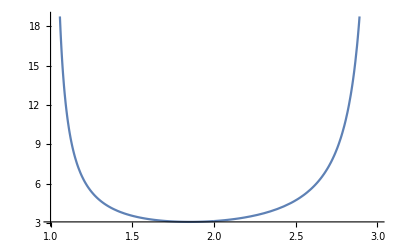

```mathematica
Plot[-2^(-1+b) Gamma[1-b] Sin[(b π)/2],{b,1,3}]
```

```mathematica
Limit[-2^(-1+b) Gamma[1-b] Sin[(b π)/2],b->2]
```

π

```mathematica
Integrate[(1-Cos[2 y])/y^b,{y,0,∞},Assumptions->b>0]
```

ConditionalExpression[-2^(-1+b) Gamma[1-b] Sin[(b π)/2], 1<b<3]

```mathematica
Series[(1-Cos[2 y])/y^b,{y,0,10},Assumptions->b>0]//Simplify
```

y^-b (2 y^2-(2 y^4)/3+(4 y^6)/45-(2 y^8)/315+(4 y^10)/14175+O[y]^11)

```mathematica
Clear[θ]
Integrate[Sin[r Exp[ⅈ θ]]^2/(r^b Exp[ⅈ b θ]),{θ,0,π},Assumptions->{1<b<3}]
```

Integrate[ⅇ^(-ⅈ b θ) r^-b Sin[ⅇ^(ⅈ θ) r]^2,{θ,0,π},Assumptions→{1<b<3}]

```mathematica
Integrate[(r^2 Exp[ⅈ θ]^2)/(r^b Exp[ⅈ b θ]),{θ,0,π},Assumptions->{1<b<3}]
```

(ⅈ (-1+ⅇ^(-ⅈ b π)) r^(2-b))/(-2+b)

```mathematica
Limit[(ⅈ (-1+ⅇ^(-ⅈ b π)) r^(2-b))/(-2+b),r->0]
```

ConditionalExpression[0, b<2]

```mathematica
<d
```

```mathematica
Integrate[(r^2 Exp[ⅈ θ]^2)/(r^b Exp[ⅈ b θ])/.b->2,{θ,0,π},Assumptions->{1<b<3}]
```

π

```mathematica
Integrate[Sin[y]^2/y^b,{y,ϵ,∞},Assumptions->{ϵ>0,b>0}]
```

ConditionalExpression[(ϵ^-b (8 ϵ^3 HypergeometricPFQ[{3/2-b/2},{3/2,5/2-b/2},-ϵ^2]+(-3+b) (2^b ϵ^b Gamma[2-b] Sin[(b π)/2]+4 ϵ Sin[ϵ]^2)))/(4 (-3+b) (-1+b)), b>1]

```mathematica
Limit[ConditionalExpression[(ϵ^-b (8 ϵ^3 HypergeometricPFQ[{3/2-b/2},{3/2,5/2-b/2},-ϵ^2]+(-3+b) (2^b ϵ^b Gamma[2-b] Sin[(b π)/2]+4 ϵ Sin[ϵ]^2)))/(4 (-3+b) (-1+b)), b>1],ϵ->0]
```

ConditionalExpression[(2^(-2+b) Gamma[2-b] Sin[(b π)/2])/(-1+b), 1<b<3]

```mathematica
Integrate[MittagLefflerE[β,β,-x^α],{x,0,∞},Assumptions->{0<β<2,α>0}]
```

Integrate[MittagLefflerE[β,β,-x^α],{x,0,∞},Assumptions→{0<β<2,α>0}]

```mathematica
Integrate[MittagLefflerE[2,2,-x^α],{x,0,∞},Assumptions->{0<β<2,α>0}]
```

ConditionalExpression[-(2 Cos[π/α] Gamma[-1+2/α])/α, 1<α<2]

```mathematica
Limit[-(2 Cos[π/α] Gamma[-1+2/α])/α,α->2]
```

π/2

```mathematica
Integrate[<dMittagLefflerE[2,2,-x^2],{x,0,∞},Assumptions->{0<β<2,α>0}]
```

π/2

```mathematica
Integrate[MittagLefflerE[2,2,-x^2],{x,0,∞},Assumptions->{0<β<2,α>0}]
```

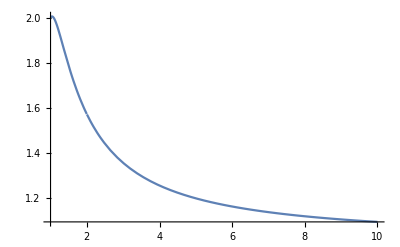

```mathematica
Plot[-(2 Cos[π/α] Gamma[-1+2/α])/α,{α,1,10},PlotRange->Full]
```

```mathematica
Limit[-(2 Cos[π/α] Gamma[-1+2/α])/α,α->∞]
```

1

```mathematica
FullSimplify[MittagLefflerE[2,2,- x],x>0]
```

Sin[√x]/(√x)

```mathematica
InverseFourierTransform[Sin[Abs[x]]/Abs[x],x,ξ]
```

√(π/2)

```mathematica
InverseFourierTransform[Sin[Abs[x]]/Abs[x]^b,x,ξ]//FullSimplify
```

-(((1-ξ)^b (1+ξ)-(-1+ξ) (1+ξ)^b) Cos[(b π)/2] Gamma[1-b])/(√(2 π) (-1+ξ^2))

```mathematica
Integrate[1/2(1-Cos[2 y])Exp[-t  y^b],{y,0,∞},Assumptions->{b>0,t>0}]
```

```mathematica
Integrate[1/2 ⅇ^(-t y^b) (1-Cos[2 y]),{y,0,∞},Assumptions->{1<b<3,t>0}]
```

Integrate[1/2 ⅇ^(-t y^b) (1-Cos[2 y]),{y,0,∞},Assumptions→{1<b<3,t>0}]

```mathematica
Integrate[1/2(1-Cos[2 y])Exp[-t  y^b]/.b->2,{y,0,∞},Assumptions->{b>0,t>0}]//FullSimplify
```

(ⅇ^(-1/t) (-1+ⅇ^(1/t)) √π)/(4 √t)

```mathematica
Integrate[(Sin[y^(1/b)]^2)/y,{y,0,∞},Assumptions->{ϵ>0,b>0}]
```

Integrate::idiv: Integral of (Sin[y^(1/b)]^2)/y does not converge on {0,∞}.

```mathematica
Integrate[(Sin[y^(1/b)]^2)/y,{y,0,∞},Assumptions->{ϵ>0,b>0}]
```

Integrate::idiv: Integral of (Sin[y^(1/b)]^2)/y does not converge on {0,∞}.

Integrate[(Sin[y^(1/b)]^2)/y,{y,0,∞},Assumptions→{ϵ>0,b>0}]

```mathematica
Integrate[(y+a)^-γ+(a-y)^-γ,{y,0,a},Assumptions->{1>γ>0,a>0}]//FullSimplify
```

(2^(1-γ) a^(1-γ))/(1-γ)

```mathematica
Now prove a lemma
```

```mathematica
Integrate[(Sin[b x^(α/2)]^2)/x^α,{x,0,∞},Assumptions->{b>0,α>1}]
```

```mathematica
(2^(2-2/α) b^(2-2/α) Cos[π/α] Gamma[-2+2/α])/α/.α->2
```

Infinity::indet: Indeterminate expression 0 b ComplexInfinity encountered.

```mathematica
Limit[(2^(2-2/α) b^(2-2/α) Cos[π/α] Gamma[-2+2/α])/α,α->2]
```

(b π)/2

```mathematica
(2^(2-2/α) b^(2-2/α) Cos[π/α] Gamma[-2+2/α])/α//TeXForm
```

\frac{2^{2-\frac{2}{\alpha }} \cos \left(\frac{\pi }{\alpha
   }\right) \Gamma \left(\frac{2}{\alpha }-2\right)
   b^{2-\frac{2}{\alpha }}}{\alpha }

```mathematica
Integrate[Exp[-ⅈ x ξ],{x,-b,b},Assumptions->b>0]
```

(2 Sin[b ξ])/ξ

```mathematica
Integrate[Exp[-x^2]Cos[x y],{x, 0, ∞},Assumptions->y>0]
```

1/2 ⅇ^(-y^2/4) √π

```mathematica
2/π Integrate[1/2 ⅇ^(-x^2/4) √π Cos[x y],{x, 0, ∞},Assumptions->y>0]
```

ⅇ^(-y^2)

```mathematica
π/(2 Gamma[2(1-1/α)]Sin[π/α])Integrate[(x+b)^(1-2/α)+(b-x)^(1-2/α),{x,0,b},Assumptions->{b>0,α>1}]//FullSimplify
```

(2^((-2+α)/α) b^(2-2/α) π Csc[π/α])/Gamma[3-2/α]

```mathematica
(2^((-2+α)/α) b^(2-2/α) π Csc[π/α])/Gamma[3-2/α]/.α->2
```

b π

```mathematica
π/(Gamma[2(1-1/α)]Sin[π/α])Integrate[(x+b)^(1-2/α),{x,0,b},Assumptions->{b>0,α>1}]//FullSimplify
```

```mathematica
-(4^(-1/α) (-4+4^(1/α)) b^(2-2/α) π Csc[π/α])/Gamma[3-2/α]
```

```mathematica
(2^((-2+α)/α) b^(2-2/α) π Csc[π/α])/Gamma[3-2/α]//TeXForm
```

\frac{\pi  2^{\frac{\alpha -2}{\alpha }} \csc \left(\frac{\pi
   }{\alpha }\right) b^{2-\frac{2}{\alpha }}}{\Gamma
   \left(3-\frac{2}{\alpha }\right)}

```mathematica
Integrate[(x+b)^(1-2/α)+(b-x)^(1-2/α),{x,0,b},Assumptions->{b>0,α>1}]//FullSimplify
```

(2^((-2+α)/α) b^(2-2/α) α)/(-1+α)

```mathematica
Integrate[(x+b)^(1-2/α),{x,0,b},Assumptions->{b>0,α>1}]//FullSimplify
```

-(2^(-(2+α)/α) (-4+4^(1/α)) b^(2-2/α) α)/(-1+α)

```mathematica
Integrate[(b-x)^(1-2/α),{x,0,b},Assumptions->{b>0,α>1}]//FullSimplify
```

(b^(2-2/α) α)/(2 (-1+α))

```mathematica
Integrate[(x+b)^(1-2/α)+(b-x)^(1-2/α),{x,0,b},Assumptions->{b>0,α>1}]//FullSimplify
```

(2^((-2+α)/α) b^(2-2/α) α)/(-1+α)

```mathematica
(-(2^(-(2+α)/α) (-4+4^(1/α)) b^(2-2/α) α)/(-1+α))/((b^(2-2/α) α)/(2 (-1+α)))//FullSimplify
```

-1+4^((-1+α)/α)

```mathematica
Lemma A.1
```

```mathematica
Integrate[(Cos[r^a]^2)/r^(b+1-d),{r,1,∞},Assumptions->{a>0,b>0,d>=1}]
```

1/(b-d)+(2^(-(a-b+d)/a) Cos[((b-d) π)/(2 a)] Gamma[(-b+d)/a])/a+(-2 a HypergeometricPFQ[{1-b/(2 a)+d/(2 a)},{3/2,2-b/(2 a)+d/(2 a)},-1]+(2 a-b+d) Sin[1]^2)/((b-d) (-2 a+b-d))

```mathematica
Integrate[(Cos[r^a]^2)/r^(b+1-d)/.b->d,{r,1,∞},Assumptions->{a>0,b>0,d>=1}]
```

Integrate::idiv: Integral of (Cos[r^a]^2)/r does not converge on {1,∞}.

Integrate[(Cos[r^a]^2)/r,{r,1,∞},Assumptions→{a>0,b>0,d≥1}]

```mathematica
Integrate[(Cos[r^a]^2)/r^(b+1-d),{r,1,∞},Assumptions->{a>0,b>d>=1}]
```

1/(b-d)+(2^(-(a-b+d)/a) Cos[((b-d) π)/(2 a)] Gamma[(-b+d)/a])/a+(-2 a HypergeometricPFQ[{1-b/(2 a)+d/(2 a)},{3/2,2-b/(2 a)+d/(2 a)},-1]+(2 a-b+d) Sin[1]^2)/((b-d) (-2 a+b-d))

```mathematica
Integrate[(Cos[r^a]^2)/r^(b+1-d),{r,1,∞},Assumptions->{a>0,0<b<d,d>=1}]
```

1/(b-d)+(2^(-(a-b+d)/a) Cos[((b-d) π)/(2 a)] Gamma[(-b+d)/a])/a+(-2 a HypergeometricPFQ[{1-b/(2 a)+d/(2 a)},{3/2,2-b/(2 a)+d/(2 a)},-1]+(2 a-b+d) Sin[1]^2)/((b-d) (-2 a+b-d))

```mathematica
Integrate[(Cos[r^a]^2)/r^(b+1-d)/.a->2,{r,1,∞},Assumptions->{a>0,0<b,d>=1}]
```

ConditionalExpression[Cos[1]^2/(b-d)+2^(1/2 (-4+b-d)) Cos[1/4 (b-d) π] Gamma[1/2 (-b+d)]-1/8 √π Gamma[1/4 (-b+d)] HypergeometricPFQRegularized[{1/4 (4-b+d)},{3/2,1/4 (8-b+d)},-1], b>d]

```mathematica
Checking Theorem 5.6
```

```mathematica
θ = 2(β+γ)-2 -(β d)/α
```

-2-(d β)/α+2 (β+γ)

```mathematica
FullSimplify[1/(θ+1)//Expand,Assumptions->{d>=1,α>0,0<β<=2,γ>0}]
```

```mathematica
α/(-d β+(2 (β+γ)-1)α)
```

```mathematica
FullSimplify[α/(-d β+(2 (β+γ)-1)α)//Expand,Assumptions->{d>=1,α>0,0<β<=2,γ>0}]
```

α/(-d β+α (-1+2 (β+γ)))

```mathematica
FullSimplify[((p t)/m)^(-(m β d)/α) ((p t)/(2 m))^(m(2β + 2γ-1))(√(2 π p/2) (p/(2 ⅇ))^(p/2))^((2m)/p-1)//Expand,Assumptions->{p>0,t>0,m>0,α>0,β>0,d>0,γ>0}]
```

2^(p/2-2 m (β+γ)) ⅇ^(-m+p/2) p^(-1/2+m+m/p-p/2) π^(-1/2+m/p) ((p t)/m)^(m (-1+(2-d/α) β+2 γ))

```mathematica
FullSimplify[2^(p/2-2 m (β+γ)) ⅇ^(-m+p/2) p^(-1/2+m+m/p-p/2) π^(-1/2+m/p) (p^(m (-1+(2-d/α) β+2 γ)) t^(m (-1+(2-d/α) β+2 γ)))/m^(m (-1+(2-d/α) β+2 γ)),Assumptions->{p>0,t>0,m>0,α>0,β>0,d>0,γ>0}]
```

2^(p/2-2 m (β+γ)) ⅇ^(-m+p/2) p^(-1/2-p/2+m (1/p+(2-d/α) β+2 γ)) π^(-1/2+m/p) (m/t)^(m (1+(-2+d/α) β-2 γ))

```mathematica
Simplify[(p^(-(m β d)/α) t^(-(m β d)/α))/m^(-(m β d)/α) ((p^(m(2β + 2γ-1)) t)/(2^(m(2β + 2γ-1)) m^(m(2β + 2γ-1))))^(m(2β + 2γ-1))(√(2 π p/2) (p/(2 ⅇ))^(p/2))^((2m)/p-1)//Expand,Assumptions->{p>0,t>0,m>0,α>0,β>0,d>0,γ>0}]
```

(2 ⅇ)^(1/2 (-2 m+p)) p^(-1/2+m+m/p-p/2) π^(-1/2+m/p) (2^(m-2 m β-2 m γ) (m/p)^(m-2 m β-2 m γ) t)^(m (-1+2 β+2 γ)) ((p t)/m)^(-(d m β)/α)

```mathematica
θ = 2(β+γ)-2-(β d)/α
1+ 1/(θ+1)//Expand//FullSimplify
```

-2-(d β)/α+2 (β+γ)

1+1/(-1-(d β)/α+2 (β+γ))

```mathematica
FullSimplify[((p t)/m)^(-(m β d)/α) ((p t)/(2 m))^(m(2β + 2γ-1))(√(2 π p/2) (p/(2 ⅇ))^(p/2))^((2m)/p)//Expand,Assumptions->{p>0,t>0,m>0,α>0,β>0,d>0,γ>0}]
```

2^(-2 m (β+γ)) ⅇ^-m p^(m (1+1/p)) π^(m/p) ((p t)/m)^(m (-1+(2-d/α) β+2 γ))

```mathematica
2^(-2 m (β+γ)) ⅇ^-m p^(m (1+1/p)) π^(m/p) (p^(m (-1+(2-d/α) β+2 γ)) t^(m (-1+(2-d/α) β+2 γ)))/m^(m (-1+(2-d/α) β+2 γ))
```

```mathematica
2^(-2 m (β+γ)) ⅇ^-m m^(-m (-1+(2-d/α) β+2 γ)) p^(m (1+1/p)+m (-1+(2-d/α) β+2 γ)) π^(m/p) t^(m (-1+(2-d/α) β+2 γ))//FullSimplify
```

2^(-2 m (β+γ)) ⅇ^-m m^(m (1+(-2+d/α) β-2 γ)) p^(m (1/p-(d β)/α+2 (β+γ))) π^(m/p) t^(m (-1+(2-d/α) β+2 γ))

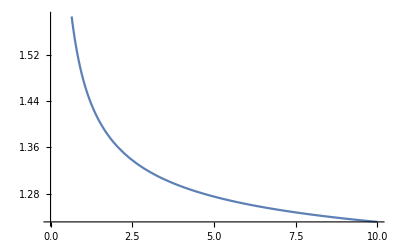

```mathematica
Plot[Exp[1/Log[12 n+1]],{n,0,10}]
```

```mathematica
Limit[Exp[1/Log[12 n+1]],n->∞]
```

1

```mathematica
Limit[Exp[1/Log[12 n+1]],n->1]//N
```

1.47679

```mathematica
Sum[t^n/(n!),{n,3,∞}]
```

1/2 (-2+2 ⅇ^t-2 t-t^2)

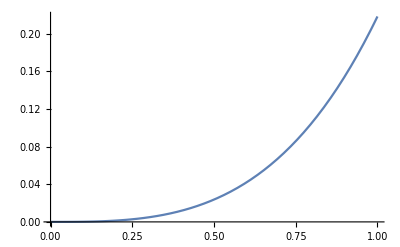

```mathematica
Plot[1/2 (-2+2 ⅇ^t-2 t-t^2),{t,0,1}]
```

```mathematica
m^m
```

```mathematica
(Exp[m] Gamma[m+1])/(√m)
```

```mathematica
2^(-2 m (β+γ)) ⅇ^-m ((Exp[m] Gamma[m+1])/(√m))^(1+(-2+d/α) β-2 γ) p^(m (1/p-(d β)/α+2 (β+γ))) π^(m/p) t^(m (-1+(2-d/α) β+2 γ))
```

```mathematica
ⅇ^-m p^(m (1/p-(d β)/α+2 (β+γ))) π^(m/p) t^(m (-1+(2-d/α) β+2 γ)) ((ⅇ^m Gamma[1+m])/(√m))^(1+(-2+d/α) β-2 γ)
```

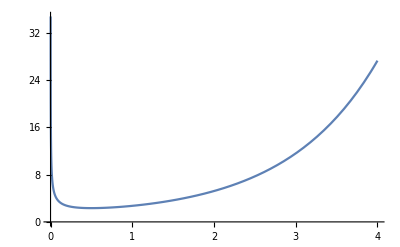

```mathematica
Plot[Exp[n]/(√n),{n,0,4}]
```

```mathematica
Slove[D[Exp[n]/(√n),n]==0,n]
```

Slove[-ⅇ^n/(2 n^(3/2))+ⅇ^n/(√n)==0,n]

```mathematica
Slove[-1/(2 n^(3/2))+1/(√n)==0,n]
```

```mathematica
Slove[-1/(2 n)+1/1==0,n]
```

```mathematica
Slove[1-1/(2  n)==0,n]
```

Slove[1-1/(2 n)==0,n]

```mathematica
Exp[1]/(2 √(2π))//N
```

0.542219

```mathematica
Clear θ
```

Clear θ

```mathematica
Sum[x^m/(m!)^(θ+1),{m,1,∞},Assumptions->(x>0,θ>0)]
```

```mathematica
Sum[x^m/(m!)^(θ+1),{m,1,∞},Assumptions->{x>0,θ>0}]
```

Sum[x^m (m!)^(-1-θ),{m,1,∞},Assumptions→{x>0,θ>0}]

```mathematica
Sum[x^m/Gamma[θ m+1],{m,1,∞},Assumptions->{x>0,θ>0}]
```

-1+MittagLefflerE[θ,x]

```mathematica
t^(m(θ+1))/m^(m(θ+1))p^(m (θ+2))/.m->(n p)/2//FullSimplify
```

2^(1/2 n p (1+θ)) p^(1/2 n p (2+θ)) (n p)^(-1/2 n p (1+θ)) t^(1/2 n p (1+θ))

```mathematica
2 √(2π m)(m/ⅇ)^m/.m->(1+θ)/2 n p
```

2^(1-1/2 n p (1+θ)) ⅇ^(-1/2 n p (1+θ)) √π (n p (1+θ))^(1/2+1/2 n p (1+θ))

```mathematica
2^(1-1/2 n p (1+θ)) ⅇ^(-1/2 n p (1+θ)) √π (n p (1+θ))^(1/2)//TeXForm
```

\sqrt{\pi } 2^{1-\frac{1}{2}
   (\theta +1) n p}
   e^{-\frac{1}{2} (\theta +1)
   n p} \sqrt{(\theta +1) n p}

```mathematica
Solve[x==t/(√n)-√n,t]
```

{{t→√n (√n+x)}}

```mathematica
(t^n Exp[-t]/.t->√n (√n+x))D[√n (√n+x),x]//FullSimplify
```

ⅇ^(-n-√n x) √n (n+√n x)^n

```mathematica
ⅇ^(-n-√n x) n^(1/2+n) (1+ x/(√n))^n
```

ⅇ^(-n-√n x) n^(1/2+n) (1+x/(√n))^n

```mathematica
Limit[ⅇ^(-√n x) (1+x/(√n))^n,n->∞]
```

ⅇ^(-x^2/2)

```mathematica
Integrate[Exp[-x^2/2],{x,0,∞}]
```

√(π/2)

```mathematica
1/2(2)^(1/(θ+1))(2 √p)^(2/(θ+1))p
```

2^(-1+3/(1+θ)) p^(1+1/(1+θ))

```mathematica
2^(-1+3/(1+θ)) p^(1+1/(1+θ))/.p->2
```

2^(4/(1+θ))

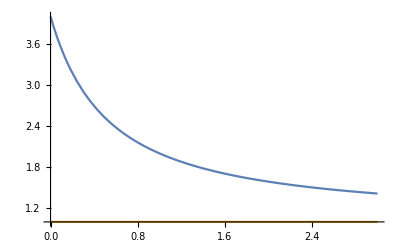

```mathematica
Plot[{2^(2/(1+θ)),1},{θ,0,3}]
```

```mathematica
Solve[2(β+γ)-2-β d/α==-1/2,β]
```

{{β→(α (-3+4 γ))/(2 (d-2 α))}}

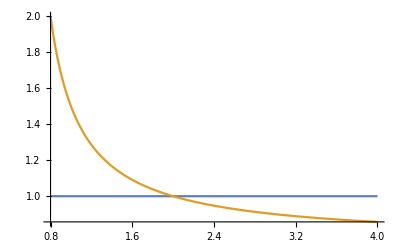

```mathematica
Plot[{1,(α (-3+4 γ))/(2 (d-2 α))/.{γ->0,d->1}},{α,4/5,4},PlotRange->Full]
```

```mathematica
(α (-3+4 γ))/(2 (d-2 α))/.{γ->0,d->1}
```

-(3 α)/(2 (1-2 α))

```mathematica
Solve[-(3 α)/(2 (1-2 α))==2,α]
```

{{α→4/5}}

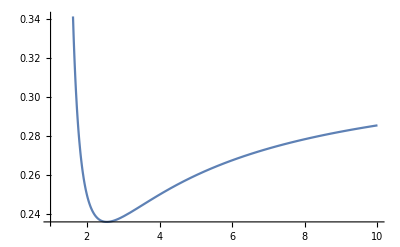

```mathematica
Plot[((λ^2 Gamma[1-1/α]Gamma[1+1/α])/(ν^(1/α)π))^(α/(α-1))/.{λ->1,ν->1},{α,1,10}]
```

```mathematica
((λ^2 Gamma[1-1/α]Gamma[1+1/α])/(ν^(1/α)π))^(α/(α-1))/.{λ->1,ν->1}//FullSimplify
```

(Csc[π/α]/α)^(α/(-1+α))

```mathematica
Limit[((λ^2 Gamma[1-1/α]Gamma[1+1/α])/(ν^(1/α)π))^(α/(α-1)),α->1]
```

$Aborted

```mathematica
((λ^2 Gamma[1-1/α]Gamma[1+1/α])/(ν^(1/α)π))^(α/(α-1))/.{λ->1,ν->1}//FullSimplify
```

```mathematica
(Csc[π/α]/α)^(α/(-1+α))
```

```mathematica
(Gamma[1-1/α]Gamma[1+1/α])/(ν^(1/α)π)//FullSimplify
```

(ν^(-1/α) Csc[π/α])/α

```mathematica
Gamma[1-1/α]Gamma[1+1/α]//FullSimplify
```

(π Csc[π/α])/α

```mathematica
((λ^2 Gamma[1-1/α]Gamma[1+1/α])/(ν^(1/α)π))^(α/(α-1))//FullSimplify
```



```mathematica
Plot[Sin[x],{x,0,10}]
```

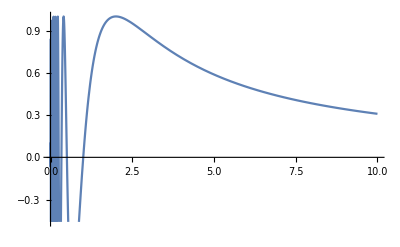

```mathematica
Plot[Sin[π/x],{x,0,10}]
```

```mathematica
|
```

```mathematica
Plot[((λ^2 Gamma[1-1/α]Gamma[1+1/α])/(ν^(1/α)π))^(α/(α-1))/.{λ->1,ν->1},{α,1,10}]
```

-Graphics-

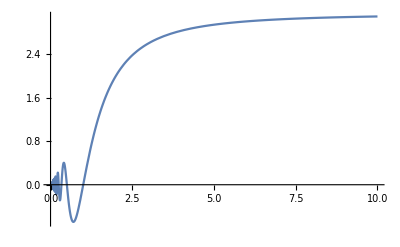

```mathematica
Plot[(x Sin[π/x])^1,{x,0,10}]
```

```mathematica
Plot[(x Sin[π/x])^(x/(1-x)),{x,1,10}]
```

-Graphics-

```mathematica
(x Sin[π/x])^(x/(1-x))/.x->2
```

1/4

```mathematica
((2^(1-1/α)λ^2)/(ν^(1/α) Sin[π/α] α))^(α/(3α-2))/.{λ->1,ν->1}
```

```mathematica
((2^(1-1/α) Csc[π/α])/α)^(α/(-2+3 α))/.α->2
```

```mathematica
1/2^(1/4)//N
```

0.840896

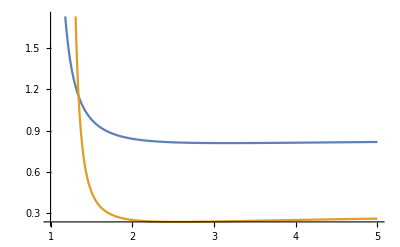

```mathematica
Plot[{((2^(1-1/α) Csc[π/α])/α)^(α/(-2+3 α)),(Csc[π/α]/α)^(α/(-1+α))},{α,1,5}]
```

```mathematica
((2^(1-1/α) Csc[π/α])/α)^(α/(-2+3 α))//FullSimplify
```

((2^((-1+α)/α) Csc[π/α])/α)^(α/(-2+3 α))

```mathematica
FullSimplify[(2^((-1+α)/α) )^(α/(-2+3 α)),Assumptions->{α>3}]
```

2^((-1+α)/(-2+3 α))

```mathematica
jkjk
```

```mathematica
((2^(1-1/α)λ^2)/(ν^(1/α) Sin[π/α] α))^(α/(3α-2))/.{λ->1,ν->2}
```

```mathematica
((2^(1-2/α) Csc[π/α])/α)^(α/(-2+3 α))/.α->2
```

```mathematica
1/(√2)//N
```

0.707107

```mathematica
FullSimplify[(2^(1-2/α) )^(α/(-2+3 α)),Assumptions->α>3]
```

2^((-2+α)/(-2+3 α))

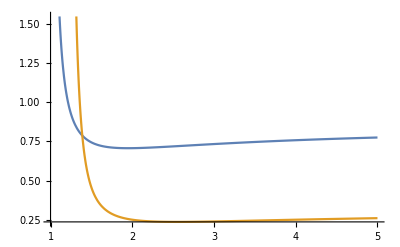

```mathematica
Plot[{((2^(1-2/α) Csc[π/α])/α)^(α/(-2+3 α)),(Csc[π/α]/α)^(α/(-1+α))},{α,1,5}]
```

```mathematica
TFSPDE
```

-2-β/2+2 Ceiling[β]

1-2/(2+β-4 Ceiling[β])

-1-β/2+2 Ceiling[β]

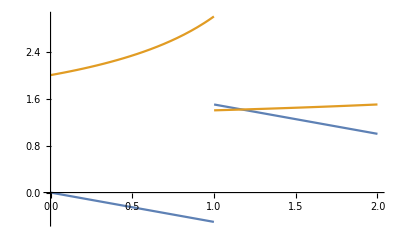

```mathematica
θ = 2(β + γ)-2 -β d/α/.{d->1,α->2,γ ->Ceiling[β]-β}//FullSimplify
(* Plot[{%,-1},{β,0,2}]*)
1+1/(1+θ)//FullSimplify
1+θ//FullSimplify
Plot[{θ,1+1/(1+θ)},{β,0,2}]
```

```mathematica
θ/.β->1.00001
1+1/(1+θ)/.β->2
```

1.5

3/2

```mathematica
1-2/(2+β-4 Ceiling[β])/.β->1.0000001
```

1.4

```mathematica
Solve[b==1+1/(1+b),b]
```

{{b→-√2},{b→√2}}

```mathematica
Integrate[MittagLefflerE[β,Ceilling[β],-x]^2,{x,0,∞},Assumptions->{0<β<1}]
```

Integrate[MittagLefflerE[β,Ceilling[β],-x]^2,{x,0,∞},Assumptions→{0<β<1}]

```mathematica
Integrate[MittagLefflerE[β,-x]^2,{x,0,∞},Assumptions->{0<β<1}]
```

Integrate[MittagLefflerE[β,-x]^2,{x,0,∞},Assumptions→{0<β<1}]

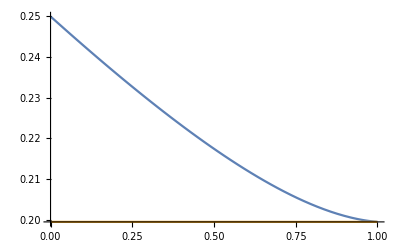

```mathematica
Plot[{NIntegrate[1/(2π)MittagLefflerE[β,-ν/2 x^2]^2/.ν->2,{x,-∞,∞}],1/(√(4π ν))/.ν->2},{β,0,1}]
```

```mathematica
1/(√(4π ν))/.ν->2
1/(√(4π ν))/.ν->2//N
```

1/(2 √(2 π))

0.199471

0.199471

```mathematica
NIntegrate[1/(2π)MittagLefflerE[1.999,2,-ν/2 x^2]^2/.ν->2,{x,-∞,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {132.64}. NIntegrate obtained 0.498306 and 0.000138939 for the integral and error estimates.

0.498306

```mathematica
NIntegrate[1/(2π)MittagLefflerE[1,1,-ν/2 x^2]^2/.ν->2,{x,-∞,∞}]
```

0.199471

```mathematica
NIntegrate[1/(2π)MittagLefflerE[2,2,-ν/2 x^2]^2/.ν->2,{x,-∞,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {132.64}. NIntegrate obtained 0.500043 and 0.000238187 for the integral and error estimates.

0.500043

```mathematica
NIntegrate[1/(2π)MittagLefflerE[2,2,-ν/2 x^2]^2/.ν->2,{x,-∞,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {132.64}. NIntegrate obtained 0.500043 and 0.000238187 for the integral and error estimates.

0.500043

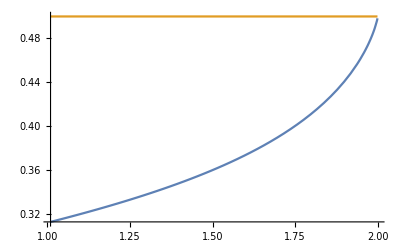

```mathematica
Plot[{NIntegrate[1/(2π)MittagLefflerE[β,2,-ν/2 x^2]^2/.ν->2,{x,-∞,∞}],1/(√(2ν))/.ν->2},{β,1.01,1.999}]
```

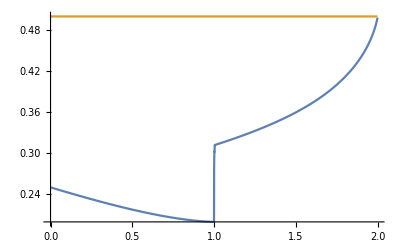

```mathematica
Plot[{NIntegrate[1/(2π)MittagLefflerE[β,Ceiling[β],-ν/2 x^2]^2/.ν->2,{x,-∞,∞}],1/(√(2ν))/.ν->2},{β,0,1.999}]
```

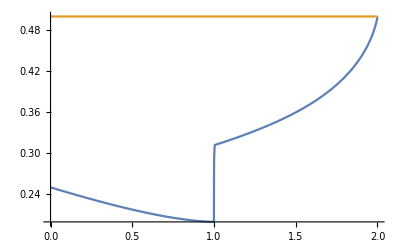

```mathematica
Plot[{NIntegrate[1/(2π)MittagLefflerE[β,Ceiling[β],-ν/2 x^2]^2/.ν->2,{x,-∞,∞}],1/(√(2ν))/.ν->2},{β,0,2}]
```

```mathematica
Round[1000* Table[{β,NIntegrate[1/(2π)MittagLefflerE[β,Ceiling[β],-ν/2 x^2]^2/.ν->2,{x,-∞,∞}]},{β,0.001,1.999,0.1}],3]/1000//N
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.00791}. NIntegrate obtained 0.292965 and 0.000382933 for the integral and error estimates.

{{0.,0.249},{0.102,0.243},{0.201,0.237},{0.3,0.228},{0.402,0.222},{0.501,0.216},{0.6,0.213},{0.702,0.207},{0.801,0.204},{0.9,0.201},{1.002,0.294},{1.101,0.321},{1.2,0.327},{1.302,0.336},{1.401,0.348},{1.5,0.36},{1.602,0.375},{1.701,0.39},{1.8,0.411},{1.902,0.441}}

```mathematica
Round[1000* Table[{β,(NIntegrate[1/(2π)MittagLefflerE[β,Ceiling[β],-ν/2 x^2]^2/.ν->2,{x,-∞,∞}] Gamma[2 Ceiling[β]-1-β])^(2/(4Ceiling[β]-1-β/2))},{β,0.001,1.999,0.1}],3]/1000//N
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.00791}. NIntegrate obtained 0.292965 and 0.000382933 for the integral and error estimates.

{{0.,0.396},{0.102,0.402},{0.201,0.411},{0.3,0.429},{0.402,0.456},{0.501,0.501},{0.6,0.573},{0.702,0.699},{0.801,0.954},{0.9,1.677},{1.002,0.684},{1.101,0.693},{1.2,0.69},{1.302,0.69},{1.401,0.69},{1.5,0.693},{1.602,0.699},{1.701,0.711},{1.8,0.726},{1.902,0.75}}

```mathematica
Plot[(NIntegrate[1/(2π)MittagLefflerE[β,Ceiling[β],-ν/2 x^2]^2/.ν->2,{x,-∞,∞}] Gamma[2 Ceiling[β]-1-β])^(2/(4Ceiling[β]-1-β/2)),{β,0.001,1.999,0.1}]
```

Plot::pllim: Range specification {β,0.001,1.999,0.1} is not of the form {x, xmin, xmax}.

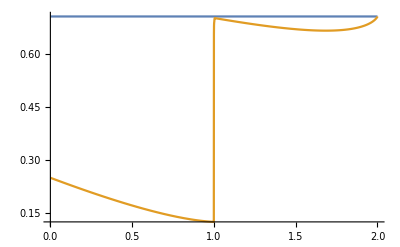

```mathematica
Plot[{1/(√2),(NIntegrate[1/(2 π)MittagLefflerE[β,Ceiling[β],1/2 (-ν) x^2]^2/.ν->2,{x,-∞,∞}] Gamma[2 Ceiling[β]-1-β/2])^(2/(4 Ceiling[β]-2-β))},{β,0.001,2},PlotRange->Full]
```

```mathematica
1/(√2)//N
```

0.707107

```mathematica
(α Sin[π/α])^(α/(1-α))/.α->3/2//N
```

0.456178

```mathematica
2^((1-α)/(2-3α))(α Sin[π/α])^(α/(2-3α))/.α->3/2//N
```

0.981822

```mathematica
NSolve[(α Sin[π/α])^(α/(1-α)) == 2^((1-α)/(2-3α))(α Sin[π/α])^(α/(2-3α)),α,Reals]
```

NSolve::incs: Warning: NSolve was unable to prove that the solution set found is complete.

{{α→1.3426},{α→ConditionalExpression[0.5/C[1], C[1]∈ℤ&&C[1]≥1.]},{α→ConditionalExpression[1/(1.+2. C[1]), C[1]∈ℤ&&C[1]≥1.]}}

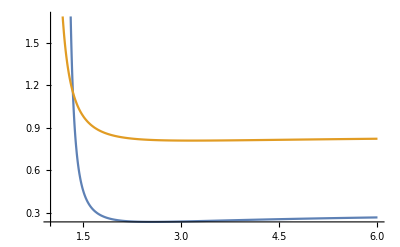

```mathematica
Plot[{(α Sin[π/α])^(α/(1-α)), 2^((1-α)/(2-3α))(α Sin[π/α])^(α/(2-3α))},{α,1.001,6}]
```

```mathematica
{(α Sin[π/α])^(α/(1-α)), 2^((1-α)/(2-3α))(α Sin[π/α])^(α/(2-3α))}/.α->1.3426 //N
```

{1.15136,1.15133}

```mathematica
2^(-1/4)//N
```

0.840896

```mathematica
j
```

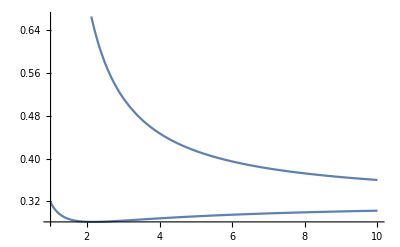

```mathematica
Plot[{2^(2-1/α)Cos[π/α] Gamma[2 (1/α-1)]/(ν^(1/α) π α),Gamma[1+1/α]/(ν^(1/α)π)}/.ν->1,{α,1,10}]
```

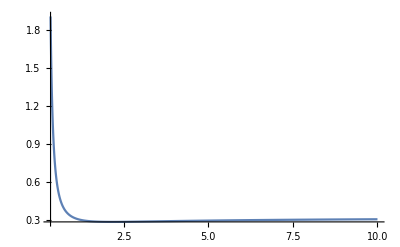

```mathematica
Plot[{Gamma[1+1/α]/(ν^(1/α)π)}/.ν->1,{α,1/3,10},PlotRange->Full]
```

```mathematica
Table[{α,2^(2-1/α)Cos[π/α] Gamma[2 (1/α-1)]/(ν^(1/α) π α)/.ν->1},{α,1.001,10,0.05}]
Table[{α,Gamma[1+1/α]/(ν^(1/α)π)/.ν->1},{α,0.001,10,0.05}]
```

{{1.001,318.897},{1.051,6.80275},{1.101,3.69062},{1.151,2.62781},{1.201,2.08675},{1.251,1.75673},{1.301,1.5333},{1.351,1.37138},{1.401,1.2483},{1.451,1.15138},{1.501,1.07295},{1.551,1.00811},{1.601,0.953559},{1.651,0.906997},{1.701,0.866769},{1.751,0.831652},{1.801,0.800723},{1.851,0.773269},{1.901,0.748734},{1.951,0.726672},{2.001,0.706727},{2.051,0.688607},{2.101,0.672074},{2.151,0.656926},{2.201,0.642998},{2.251,0.630149},{2.301,0.618257},{2.351,0.60722},{2.401,0.59695},{2.451,0.58737},{2.501,0.578413},{2.551,0.57002},{2.601,0.56214},{2.651,0.554728},{2.701,0.547744},{2.751,0.541151},{2.801,0.534919},{2.851,0.529018},{2.901,0.523424},{2.951,0.518113},{3.001,0.513064},{3.051,0.508258},{3.101,0.503679},{3.151,0.499311},{3.201,0.49514},{3.251,0.491153},{3.301,0.487338},{3.351,0.483685},{3.401,0.480183},{3.451,0.476823},{3.501,0.473597},{3.551,0.470498},{3.601,0.467517},{3.651,0.464649},{3.701,0.461886},{3.751,0.459225},{3.801,0.456658},{3.851,0.454182},{3.901,0.451791},{3.951,0.449481},{4.001,0.447248},{4.051,0.445089},{4.101,0.443},{4.151,0.440977},{4.201,0.439018},{4.251,0.437119},{4.301,0.435279},{4.351,0.433493},{4.401,0.43176},{4.451,0.430078},{4.501,0.428444},{4.551,0.426857},{4.601,0.425314},{4.651,0.423813},{4.701,0.422354},{4.751,0.420934},{4.801,0.419551},{4.851,0.418205},{4.901,0.416893},{4.951,0.415615},{5.001,0.414369},{5.051,0.413155},{5.101,0.41197},{5.151,0.410814},{5.201,0.409686},{5.251,0.408584},{5.301,0.407509},{5.351,0.406458},{5.401,0.405432},{5.451,0.404429},{5.501,0.403449},{5.551,0.40249},{5.601,0.401553},{5.651,0.400635},{5.701,0.399738},{5.751,0.39886},{5.801,0.398},{5.851,0.397158},{5.901,0.396334},{5.951,0.395526},{6.001,0.394735},{6.051,0.39396},{6.101,0.3932},{6.151,0.392455},{6.201,0.391725},{6.251,0.391008},{6.301,0.390306},{6.351,0.389616},{6.401,0.38894},{6.451,0.388276},{6.501,0.387625},{6.551,0.386985},{6.601,0.386357},{6.651,0.38574},{6.701,0.385134},{6.751,0.384539},{6.801,0.383955},{6.851,0.38338},{6.901,0.382815},{6.951,0.38226},{7.001,0.381714},{7.051,0.381178},{7.101,0.38065},{7.151,0.380131},{7.201,0.379621},{7.251,0.379119},{7.301,0.378625},{7.351,0.378139},{7.401,0.37766},{7.451,0.377189},{7.501,0.376726},{7.551,0.376269},{7.601,0.37582},{7.651,0.375378},{7.701,0.374942},{7.751,0.374513},{7.801,0.37409},{7.851,0.373673},{7.901,0.373263},{7.951,0.372858},{8.001,0.37246},{8.051,0.372067},{8.101,0.37168},{8.151,0.371298},{8.201,0.370922},{8.251,0.37055},{8.301,0.370185},{8.351,0.369824},{8.401,0.369468},{8.451,0.369117},{8.501,0.36877},{8.551,0.368429},{8.601,0.368092},{8.651,0.367759},{8.701,0.367431},{8.751,0.367107},{8.801,0.366787},{8.851,0.366472},{8.901,0.36616},{8.951,0.365853},{9.001,0.365549},{9.051,0.365249},{9.101,0.364953},{9.151,0.364661},{9.201,0.364372},{9.251,0.364087},{9.301,0.363805},{9.351,0.363527},{9.401,0.363252},{9.451,0.362981},{9.501,0.362712},{9.551,0.362447},{9.601,0.362185},{9.651,0.361926},{9.701,0.36167},{9.751,0.361417},{9.801,0.361167},{9.851,0.36092},{9.901,0.360676},{9.951,0.360434}}

{{0.001,1.28083842957023×10^2567},{0.051,2.37785×10^17},{0.101,915572.},{0.151,756.883},{0.201,36.612},{0.251,7.45847},{0.301,2.90413},{0.351,1.58509},{0.401,1.05061},{0.451,0.78506},{0.501,0.634281},{0.551,0.540386},{0.601,0.477885},{0.651,0.434158},{0.701,0.402377},{0.751,0.378577},{0.801,0.360324},{0.851,0.346053},{0.901,0.334717},{0.951,0.325596},{1.001,0.318176},{1.051,0.312085},{1.101,0.307049},{1.151,0.302859},{1.201,0.299356},{1.251,0.296415},{1.301,0.293938},{1.351,0.291848},{1.401,0.290083},{1.451,0.28859},{1.501,0.28733},{1.551,0.286266},{1.601,0.285372},{1.651,0.284623},{1.701,0.283999},{1.751,0.283483},{1.801,0.283061},{1.851,0.282721},{1.901,0.282452},{1.951,0.282245},{2.001,0.282092},{2.051,0.281987},{2.101,0.281924},{2.151,0.281898},{2.201,0.281904},{2.251,0.281938},{2.301,0.281997},{2.351,0.282078},{2.401,0.282178},{2.451,0.282295},{2.501,0.282428},{2.551,0.282573},{2.601,0.282729},{2.651,0.282896},{2.701,0.283071},{2.751,0.283254},{2.801,0.283443},{2.851,0.283638},{2.901,0.283838},{2.951,0.284041},{3.001,0.284248},{3.051,0.284458},{3.101,0.28467},{3.151,0.284884},{3.201,0.2851},{3.251,0.285316},{3.301,0.285533},{3.351,0.285751},{3.401,0.285968},{3.451,0.286186},{3.501,0.286403},{3.551,0.286619},{3.601,0.286835},{3.651,0.28705},{3.701,0.287264},{3.751,0.287477},{3.801,0.287689},{3.851,0.287899},{3.901,0.288108},{3.951,0.288315},{4.001,0.288521},{4.051,0.288725},{4.101,0.288928},{4.151,0.289129},{4.201,0.289328},{4.251,0.289525},{4.301,0.289721},{4.351,0.289915},{4.401,0.290106},{4.451,0.290297},{4.501,0.290485},{4.551,0.290671},{4.601,0.290856},{4.651,0.291038},{4.701,0.291219},{4.751,0.291398},{4.801,0.291575},{4.851,0.291751},{4.901,0.291924},{4.951,0.292096},{5.001,0.292266},{5.051,0.292434},{5.101,0.2926},{5.151,0.292764},{5.201,0.292927},{5.251,0.293088},{5.301,0.293247},{5.351,0.293405},{5.401,0.293561},{5.451,0.293715},{5.501,0.293867},{5.551,0.294018},{5.601,0.294167},{5.651,0.294315},{5.701,0.294461},{5.751,0.294605},{5.801,0.294748},{5.851,0.29489},{5.901,0.29503},{5.951,0.295168},{6.001,0.295305},{6.051,0.29544},{6.101,0.295574},{6.151,0.295707},{6.201,0.295838},{6.251,0.295968},{6.301,0.296097},{6.351,0.296224},{6.401,0.296349},{6.451,0.296474},{6.501,0.296597},{6.551,0.296719},{6.601,0.29684},{6.651,0.296959},{6.701,0.297077},{6.751,0.297194},{6.801,0.29731},{6.851,0.297424},{6.901,0.297538},{6.951,0.29765},{7.001,0.297761},{7.051,0.297871},{7.101,0.29798},{7.151,0.298088},{7.201,0.298195},{7.251,0.2983},{7.301,0.298405},{7.351,0.298509},{7.401,0.298611},{7.451,0.298713},{7.501,0.298813},{7.551,0.298913},{7.601,0.299012},{7.651,0.299109},{7.701,0.299206},{7.751,0.299302},{7.801,0.299397},{7.851,0.299491},{7.901,0.299584},{7.951,0.299676},{8.001,0.299768},{8.051,0.299858},{8.101,0.299948},{8.151,0.300037},{8.201,0.300125},{8.251,0.300212},{8.301,0.300299},{8.351,0.300384},{8.401,0.300469},{8.451,0.300553},{8.501,0.300637},{8.551,0.300719},{8.601,0.300801},{8.651,0.300882},{8.701,0.300962},{8.751,0.301042},{8.801,0.301121},{8.851,0.301199},{8.901,0.301277},{8.951,0.301354},{9.001,0.30143},{9.051,0.301506},{9.101,0.30158},{9.151,0.301655},{9.201,0.301728},{9.251,0.301801},{9.301,0.301874},{9.351,0.301945},{9.401,0.302017},{9.451,0.302087},{9.501,0.302157},{9.551,0.302226},{9.601,0.302295},{9.651,0.302363},{9.701,0.302431},{9.751,0.302498},{9.801,0.302565},{9.851,0.302631},{9.901,0.302696},{9.951,0.302761}}

```mathematica
Gamma[1+1/α]/(ν^(1/α)π)/.{ν->1,α->1}
Gamma[1+1/α]/(ν^(1/α)π)/.{ν->1,α->1}//N
Gamma[1+1/α]/(ν^(1/α)π)/.{ν->1,α->2}`
Gamma[1+1/α]/(ν^(1/α)π)/.{ν->1,α->2}//N
```

1/π

0.31831

1/(2 √π)

0.282095

```mathematica
2^(2-1/α)Cos[π/α] Gamma[2 (1/α-1)]/(ν^(1/α) π α)/.{ν->1,α->2}
```

Infinity::indet: Indeterminate expression (0 2 √2 ComplexInfinity)/π encountered.

Indeterminate

```mathematica
Limit[2^(2-1/α)Cos[π/α] Gamma[2 (1/α-1)]/(ν^(1/α) π α)/.ν->1,α->2]
```

1/(√2)

```mathematica
SHE-SWE
```

```mathematica
θ = 2β-2-β/2
θ+1
1+1/(1+θ)//FullSimplify
(2+θ)/(1+θ)//Simplify
1/(1+θ)//FullSimplify
```

-2+(3 β)/2

-1+(3 β)/2

(3 β)/(-2+3 β)

(3 β)/(-2+3 β)

2/(-2+3 β)

```mathematica
Solve[2β-2-β/2 == -1,β]
```

{{β→2/3}}

```mathematica
Integrate[1/π MittagLefflerE[β,β,-x^2]^2,{x,0,∞},Assumptions->{0<β<2}]
```

Integrate[(MittagLefflerE[β,β,-x^2]^2)/π,{x,0,∞},Assumptions→{0<β<2}]

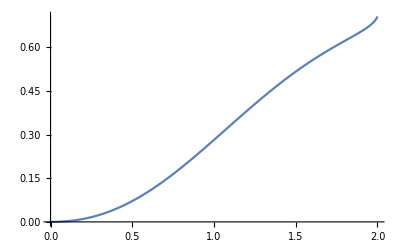

```mathematica
Plot[NIntegrate[1/π MittagLefflerE[β,β,-x^2/2]^2,{x,0,∞}],{β,0,2}]
```

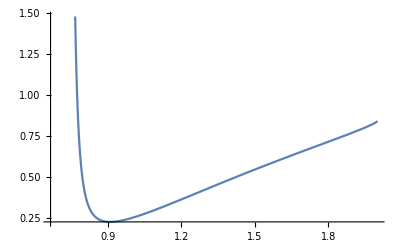

```mathematica
Plot[(NIntegrate[1/π MittagLefflerE[β,β,-x^2/2]^2,{x,0,∞}] Gamma[-1+(3β)/2])^(2/(3β-2)),{β,0.667,2}]
```

```mathematica
Table[{β,(NIntegrate[1/π MittagLefflerE[β,β,-x^2]^2,{x,0,∞}] Gamma[-1+(3β)/2])^(2/(3β-2))},{β,0.736,1.999,0.05}]
Table[{β,NIntegrate[1/π MittagLefflerE[β,β,-x^2]^2,{x,0,∞}] },{β,0.001,1.999,0.05}]
```

{{0.736,1.24849},{0.786,0.096651},{0.836,0.0716422},{0.886,0.0796926},{0.936,0.0967048},{0.986,0.118356},{1.036,0.142986},{1.086,0.169652},{1.136,0.19771},{1.186,0.226689},{1.236,0.256233},{1.286,0.28607},{1.336,0.315996},{1.386,0.345859},{1.436,0.375549},{1.486,0.404989},{1.536,0.434133},{1.586,0.46296},{1.636,0.491473},{1.686,0.519702},{1.736,0.547706},{1.786,0.57559},{1.836,0.603531},{1.886,0.631856},{1.936,0.661276},{1.986,0.694367}}

{{0.001,1.56385×10^-7},{0.051,0.000423902},{0.101,0.00172608},{0.151,0.00399104},{0.201,0.00728983},{0.251,0.0116789},{0.301,0.017199},{0.351,0.0238748},{0.401,0.0317146},{0.451,0.0407103},{0.501,0.0508381},{0.551,0.0620589},{0.601,0.0743194},{0.651,0.0875533},{0.701,0.101683},{0.751,0.116619},{0.801,0.132267},{0.851,0.148521},{0.901,0.165273},{0.951,0.182411},{1.001,0.210687},{1.051,0.217389},{1.101,0.235001},{1.151,0.25255},{1.201,0.269929},{1.251,0.287042},{1.301,0.303796},{1.351,0.32011},{1.401,0.335912},{1.451,0.351144},{1.501,0.365758},{1.551,0.379725},{1.601,0.393035},{1.651,0.4057},{1.701,0.417765},{1.751,0.429319},{1.801,0.440523},{1.851,0.451663},{1.901,0.463304},{1.951,0.476828}}

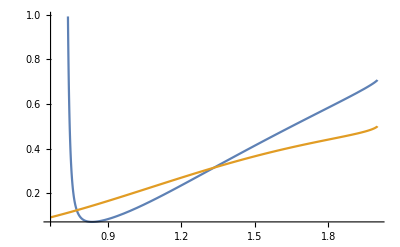

```mathematica
Plot[{(NIntegrate[1/π MittagLefflerE[β,β,-x^2]^2,{x,0,∞}] Gamma[-1+(3β)/2])^(2/(3β-2)),NIntegrate[1/π MittagLefflerE[β,β,-x^2]^2,{x,0,∞}]},{β,0.667,2}]
```

```mathematica
(NIntegrate[1/π MittagLefflerE[β,β,-x^2/2]^2,{x,0,∞}] Gamma[-1+(3β)/2])^(2/(3β-2))/.β->1
```

0.25

```mathematica
(NIntegrate[1/π MittagLefflerE[β,β,-x^2/2]^2,{x,0,∞}] Gamma[-1+(3β)/2])^(2/(3β-2))/.β->2
2^(-1/4)//N
```

0.840649

0.840896

```mathematica
NIntegrate[1/π MittagLefflerE[β,β,-x^2/2]^2,{x,0,∞}] /.β->1
1/(√(4π))//N
NIntegrate[1/π MittagLefflerE[β,β,-x^2/2]^2,{x,0,∞}] /.β->2
1/(√2)//N
NIntegrate[1/π MittagLefflerE[β,β,-x^2/2]^2,{x,0,∞}] /.β->2/3
```

0.282095

0.282095

0.706691

0.707107

0.129949

```mathematica
1/(√(4π))//N
```

0.282095

```mathematica
FullSimplify[1< 4 + 2/β Min[2(Ceiling[β]-β)-1,0],Assumptions->{0<β<2}]
```

True

```mathematica
1< 4 + 2/β Min[2(Ceiling[β]-β)-1,0]//FullSimplify
```

β (3 β+2 Min[0,-1-2 β+2 Ceiling[β]])>0

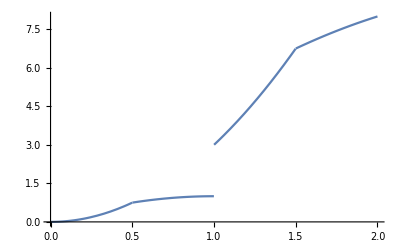

```mathematica
Plot[{β (3 β+2 Min[0,-1-2 β+2 Ceiling[β]])},{β,0,2}]
```

```mathematica
Plot[{2 (Ceiling[β]-1)-β/2,1+1/(2 Ceiling[β]-1-β/2)},{β,0,2}]
res = Table[{β,2 (Ceiling[β]-1)-β/2,1+1/(2 Ceiling[β]-1-β/2)},{β,0,2,0.05}]
```

-Graphics-

{{0.,-2.,0.},{0.05,-0.025,2.02564},{0.1,-0.05,2.05263},{0.15,-0.075,2.08108},{0.2,-0.1,2.11111},{0.25,-0.125,2.14286},{0.3,-0.15,2.17647},{0.35,-0.175,2.21212},{0.4,-0.2,2.25},{0.45,-0.225,2.29032},{0.5,-0.25,2.33333},{0.55,-0.275,2.37931},{0.6,-0.3,2.42857},{0.65,-0.325,2.48148},{0.7,-0.35,2.53846},{0.75,-0.375,2.6},{0.8,-0.4,2.66667},{0.85,-0.425,2.73913},{0.9,-0.45,2.81818},{0.95,-0.475,2.90476},{1.,-0.5,3.},{1.05,1.475,1.40404},{1.1,1.45,1.40816},{1.15,1.425,1.41237},{1.2,1.4,1.41667},{1.25,1.375,1.42105},{1.3,1.35,1.42553},{1.35,1.325,1.43011},{1.4,1.3,1.43478},{1.45,1.275,1.43956},{1.5,1.25,1.44444},{1.55,1.225,1.44944},{1.6,1.2,1.45455},{1.65,1.175,1.45977},{1.7,1.15,1.46512},{1.75,1.125,1.47059},{1.8,1.1,1.47619},{1.85,1.075,1.48193},{1.9,1.05,1.4878},{1.95,1.025,1.49383},{2.,1.,1.5}}

```mathematica
2 (Ceiling[β]-1)-β/2/.β->1.001
```

1.4995